```mathematica
Clear[x,L]
mat = Outer[Times,{1-4x/L,4x/L},{1-4 x/L,4x/L} ]
```

{{(1-(4 x)/L)^2,(4 x (1-(4 x)/L))/L},{(4 x (1-(4 x)/L))/L,(16 x^2)/L^2}}

```mathematica
% //MatrixForm
```

((1-(4 x)/L)^2 | (4 x (1-(4 x)/L))/L
(4 x (1-(4 x)/L))/L | (16 x^2)/L^2)

```mathematica
dN = {-4/L,4/L}
```

{-4/L,4/L}

```mathematica
mat.dN
```

{(16 x (1-(4 x)/L))/L^2-(4 (1-(4 x)/L)^2)/L,(64 x^2)/L^3-(16 x (1-(4 x)/L))/L^2}

```mathematica
Integrate[%,{x,0,L}]
```

{-68/3,104/3}

```mathematica
L=1;
N1[x_]:= Piecewise[{{1-4x / L,0≤x≤ L/4},{0,_}}];
N2[x_] := Piecewise[ {{4x/L,0≤ x ≤ L/4},{(2L-4x)/L,L/4≤ x≤ L/2}}];
N3[x_] := Piecewise[ {{(4x-L)/L,L/4≤ x≤ L/2},{(3L-4x)/L,L/2≤ x≤ 3L/4}}];
N4[x_] := Piecewise[ {{(4x-2L)/L,L/2≤ x≤ 3L/4},{(4L-4x)/L,3L/4≤ x≤ L}}];
N5[x_] := Piecewise[ {{(4x-3L)/L,3L/4≤ x≤ L},{0, _}}];
```

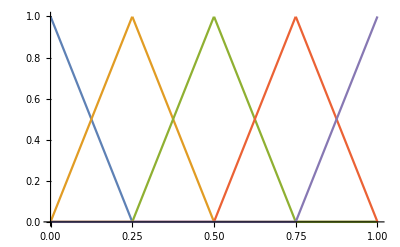

```mathematica
Plot[{N1[x],N2[x],N3[x],N4[x],N5[x]},{x,0,L}]
```

```mathematica
With[{L=1},N3[L/2]]
```

Piecewise[{{(2-L)/L, L/4≤1/2≤L/2}, {(-2+4 L)/L, L/2≤1/2≤(3 L)/4}, {0, True}}]

```mathematica
𝒩={N1[x],N2[x],N3[x],N4[x],N5[x]};
```

The second term is equal: ∑_(j=1)^5 ∑_(k=1)^5 ∫N_i N_k dN_j/dx u_k u_j

This the the term Ni Nk:

```mathematica
ℳ = Outer[Times,𝒩,𝒩]// Simplify
```

{{(Piecewise[{{1-4 x, 0≤x≤1/4}, {0, True}}])^2,Piecewise[{{-4 x (-1+4 x), 0≤x≤1/4}, {0, True}}],0,0,0},{Piecewise[{{-4 x (-1+4 x), 0≤x≤1/4}, {0, True}}],(Piecewise[{{4 x, 0≤x≤1/4}, {2-4 x, 1/4≤x≤1/2}, {0, True}}])^2,Piecewise[{{-2 (1-6 x+8 x^2), 1/4≤x≤1/2}, {0, True}}],0,0},{0,Piecewise[{{-2 (1-6 x+8 x^2), 1/4≤x≤1/2}, {0, True}}],(Piecewise[{{-1+4 x, 1/4≤x≤1/2}, {3-4 x, 1/2≤x≤3/4}, {0, True}}])^2,Piecewise[{{-6+20 x-16 x^2, 1/2≤x≤3/4}, {0, True}}],0},{0,0,Piecewise[{{-6+20 x-16 x^2, 1/2≤x≤3/4}, {0, True}}],(Piecewise[{{-2+4 x, 1/2≤x≤3/4}, {4-4 x, 3/4≤x≤1}, {0, True}}])^2,Piecewise[{{-4 (-1+x) (-3+4 x), 3/4≤x≤1}, {0, True}}]},{0,0,0,Piecewise[{{-4 (-1+x) (-3+4 x), 3/4≤x≤1}, {0, True}}],(Piecewise[{{-3+4 x, 3/4≤x≤1}, {0, True}}])^2}}

Now comes the part dN_j/dx

```mathematica
d𝒩=D[𝒩,{x}] // Simplify
```

{Piecewise[{{-4, 0<x<1/4}, {0, x>1/4||x<0}, {Indeterminate, True}}],Piecewise[{{-4, 1/4<x<1/2}, {4, 0<x<1/4}, {0, x>1/2||x<0}, {Indeterminate, True}}],Piecewise[{{-4, 1/2<x<3/4}, {4, 1/4<x<1/2}, {0, x>3/4||x<1/4}, {Indeterminate, True}}],Piecewise[{{-4, 3/4<x<1}, {4, 1/2<x<3/4}, {0, x>1||x<1/2}, {Indeterminate, True}}],Piecewise[{{4, 3/4<x<1}, {0, x>1||x<3/4}, {Indeterminate, True}}]}

```mathematica
u = {u1,u2,u3,u4,u5};
```

```mathematica
umat= Outer[Times,u,u]
```

{{u1^2,u1 u2,u1 u3,u1 u4,u1 u5},{u1 u2,u2^2,u2 u3,u2 u4,u2 u5},{u1 u3,u2 u3,u3^2,u3 u4,u3 u5},{u1 u4,u2 u4,u3 u4,u4^2,u4 u5},{u1 u5,u2 u5,u3 u5,u4 u5,u5^2}}

```mathematica
d𝒩.%//Simplify
```

Piecewise[{{16 (u1-u2)^2, 0<x<1/4}, {16 (u2-u3)^2, 1/4<x<1/2}, {16 (u3-u4)^2, 1/2<x<3/4}, {16 (u4-u5)^2, 3/4<x<1}, {0, x>1||x<0}, {Indeterminate, True}}]

```mathematica
𝒩.Outer[Times,𝒩,d𝒩].umat//Simplify
```

{Piecewise[{{-4 u1 (u4-u5) (25-56 x+32 x^2), 3/4<x<1}, {-4 u1 (u3-u4) (13-40 x+32 x^2), 1/2<x<3/4}, {-4 u1 (u2-u3) (5-24 x+32 x^2), 1/4<x<1/2}, {-4 u1 (u1-u2) (1-8 x+32 x^2), 0<x<1/4}, {0, x>1||x<0}, {Indeterminate, True}}],Piecewise[{{-4 u2 (u4-u5) (25-56 x+32 x^2), 3/4<x<1}, {-4 u2 (u3-u4) (13-40 x+32 x^2), 1/2<x<3/4}, {-4 u2 (u2-u3) (5-24 x+32 x^2), 1/4<x<1/2}, {4 u2 (-u1+u2) (1-8 x+32 x^2), 0<x<1/4}, {0, x>1||x<0}, {Indeterminate, True}}],Piecewise[{{-4 u3 (u4-u5) (25-56 x+32 x^2), 3/4<x<1}, {-4 u3 (u3-u4) (13-40 x+32 x^2), 1/2<x<3/4}, {4 u3 (-u2+u3) (5-24 x+32 x^2), 1/4<x<1/2}, {-4 (u1-u2) u3 (1-8 x+32 x^2), 0<x<1/4}, {0, x>1||x<0}, {Indeterminate, True}}],Piecewise[{{-4 u4 (u4-u5) (25-56 x+32 x^2), 3/4<x<1}, {4 u4 (-u3+u4) (13-40 x+32 x^2), 1/2<x<3/4}, {-4 (u2-u3) u4 (5-24 x+32 x^2), 1/4<x<1/2}, {-4 (u1-u2) u4 (1-8 x+32 x^2), 0<x<1/4}, {0, x>1||x<0}, {Indeterminate, True}}],Piecewise[{{4 u5 (-u4+u5) (25-56 x+32 x^2), 3/4<x<1}, {-4 (u3-u4) u5 (13-40 x+32 x^2), 1/2<x<3/4}, {-4 (u2-u3) u5 (5-24 x+32 x^2), 1/4<x<1/2}, {-4 (u1-u2) u5 (1-8 x+32 x^2), 0<x<1/4}, {0, x>1||x<0}, {Indeterminate, True}}]}

```mathematica
Evaluate[Integrate[%,{x,0,L}]]
```

{-2/3 (u1^2-u1 u5),-2/3 (u1 u2-u2 u5),-2/3 (u1 u3-u3 u5),-2/3 (u1 u4-u4 u5),-2/3 (u1 u5-u5^2)}

```mathematica
Outer[Times,𝒩,d𝒩]//Simplify
```

{{Piecewise[{{-4+16 x, 0<x<1/4}, {0, 4 x>1||x<0}, {Indeterminate, True}}],Piecewise[{{4-16 x, 0<x<1/4}, {0, 1/4<x<1/2||2 x>1||x<0}, {Indeterminate, True}}],Piecewise[{{0, 4 x<1||1/4<x<1/2||1/2<x<3/4||4 x>3}, {Indeterminate, True}}],Piecewise[{{0, 2 x<1||1/2<x<3/4||3/4<x<1||x>1}, {Indeterminate, True}}],Piecewise[{{0, 4 x<3||3/4<x<1||x>1}, {Indeterminate, True}}]},{Piecewise[{{-16 x, 0<x<1/4}, {0, 4 x>1||x<0}, {Indeterminate, True}}],Piecewise[{{16 x, 0<x<1/4}, {-8+16 x, 1/4<x<1/2}, {0, 2 x>1||x<0}, {Indeterminate, True}}],Piecewise[{{8-16 x, 1/4<x<1/2}, {0, 4 x<1||1/2<x<3/4||4 x>3}, {Indeterminate, True}}],Piecewise[{{0, 2 x<1||1/2<x<3/4||3/4<x<1||x>1}, {Indeterminate, True}}],Piecewise[{{0, 4 x<3||3/4<x<1||x>1}, {Indeterminate, True}}]},{Piecewise[{{0, 0<x<1/4||4 x>1||x<0}, {Indeterminate, True}}],Piecewise[{{4-16 x, 1/4<x<1/2}, {0, 0<x<1/4||2 x>1||x<0}, {Indeterminate, True}}],Piecewise[{{4 (-3+4 x), 1/2<x<3/4}, {-4+16 x, 1/4<x<1/2}, {0, 4 x>3||4 x<1}, {Indeterminate, True}}],Piecewise[{{12-16 x, 1/2<x<3/4}, {0, 2 x<1||3/4<x<1||x>1}, {Indeterminate, True}}],Piecewise[{{0, 4 x<3||3/4<x<1||x>1}, {Indeterminate, True}}]},{Piecewise[{{0, 0<x<1/4||4 x>1||x<0}, {Indeterminate, True}}],Piecewise[{{0, 0<x<1/4||1/4<x<1/2||2 x>1||x<0}, {Indeterminate, True}}],Piecewise[{{8-16 x, 1/2<x<3/4}, {0, 1/4<x<1/2||4 x>3||4 x<1}, {Indeterminate, True}}],Piecewise[{{16 (-1+x), 3/4<x<1}, {-8+16 x, 1/2<x<3/4}, {0, x>1||2 x<1}, {Indeterminate, True}}],Piecewise[{{-16 (-1+x), 3/4<x<1}, {0, 4 x<3||x>1}, {Indeterminate, True}}]},{Piecewise[{{0, 0<x<1/4||4 x>1||x<0}, {Indeterminate, True}}],Piecewise[{{0, 0<x<1/4||1/4<x<1/2||2 x>1||x<0}, {Indeterminate, True}}],Piecewise[{{0, 1/4<x<1/2||1/2<x<3/4||4 x>3||4 x<1}, {Indeterminate, True}}],Piecewise[{{12-16 x, 3/4<x<1}, {0, 1/2<x<3/4||x>1||2 x<1}, {Indeterminate, True}}],Piecewise[{{4 (-3+4 x), 3/4<x<1}, {0, x>1||4 x<3}, {Indeterminate, True}}]}}

```mathematica
𝒩.% //Simplify
```

{Piecewise[{{-4 (1-8 x+32 x^2), 0<x<1/4}, {0, 4 x>1||x<0}, {Indeterminate, True}}],Piecewise[{{-4 (5-24 x+32 x^2), 1/4<x<1/2}, {4 (1-8 x+32 x^2), 0<x<1/4}, {0, 2 x>1||x<0}, {Indeterminate, True}}],Piecewise[{{-4 (13-40 x+32 x^2), 1/2<x<3/4}, {4 (5-24 x+32 x^2), 1/4<x<1/2}, {0, 4 x<1||4 x>3}, {Indeterminate, True}}],Piecewise[{{-4 (25-56 x+32 x^2), 3/4<x<1}, {4 (13-40 x+32 x^2), 1/2<x<3/4}, {0, 2 x<1||x>1}, {Indeterminate, True}}],Piecewise[{{4 (25-56 x+32 x^2), 3/4<x<1}, {0, 4 x<3||x>1}, {Indeterminate, True}}]}

```mathematica
int = Evaluate[Integrate[%,{x,0,L}]] //Simplify
```

{-2/3,0,0,0,2/3}

```mathematica
Outer[Times,int,int]
```

{{4/9,0,0,0,-4/9},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{-4/9,0,0,0,4/9}}

```mathematica
Dimensions[%]
```

{5}

```mathematica
% //MatrixForm
```

((-1/4 | 1/4 | 0 | 0 | 0
-1/12 | 1/12 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0) | (-1/12 | 1/12 | 0 | 0 | 0
-1/12 | 1/12 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)
(-1/12 | 1/12 | 0 | 0 | 0
-1/12 | 1/12 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0) | (-1/12 | 1/12 | 0 | 0 | 0
-1/4 | 0 | 1/4 | 0 | 0
0 | -1/12 | 1/12 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0
0 | -1/12 | 1/12 | 0 | 0
0 | -1/12 | 1/12 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)
(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0
0 | -1/12 | 1/12 | 0 | 0
0 | -1/12 | 1/12 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0
0 | -1/12 | 1/12 | 0 | 0
0 | -1/4 | 0 | 1/4 | 0
0 | 0 | -1/12 | 1/12 | 0
0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | -1/12 | 1/12 | 0
0 | 0 | -1/12 | 1/12 | 0
0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)
(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | -1/12 | 1/12 | 0
0 | 0 | -1/12 | 1/12 | 0
0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | -1/12 | 1/12 | 0
0 | 0 | -1/4 | 0 | 1/4
0 | 0 | 0 | -1/12 | 1/12) | (0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1/12 | 1/12
0 | 0 | 0 | -1/12 | 1/12)
(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1/12 | 1/12
0 | 0 | 0 | -1/12 | 1/12) | (0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1/12 | 1/12
0 | 0 | 0 | -1/4 | 1/4))

```mathematica
Outer[Times,d𝒩,d𝒩]//Simplify
```

{{Piecewise[{{16, 0<x<1/4}, {0, 4 x>1||x<0}, {Indeterminate, True}}],Piecewise[{{-16, 0<x<1/4}, {0, 1/4<x<1/2||2 x>1||x<0}, {Indeterminate, True}}],Piecewise[{{0, 0<x<1/4||1/4<x<1/2||1/2<x<3/4||4 x>3||x<0}, {Indeterminate, True}}],Piecewise[{{0, 0<x<1/4||1/4<x<1/2||1/2<x<3/4||3/4<x<1||x>1||x<0}, {Indeterminate, True}}],Piecewise[{{0, 0<x<1/4||1/4<x<3/4||3/4<x<1||x>1||x<0}, {Indeterminate, True}}]},{Piecewise[{{-16, 0<x<1/4}, {0, 1/4<x<1/2||2 x>1||x<0}, {Indeterminate, True}}],Piecewise[{{16, 0<x<1/4||1/4<x<1/2}, {0, 2 x>1||x<0}, {Indeterminate, True}}],Piecewise[{{-16, 1/4<x<1/2}, {0, 0<x<1/4||1/2<x<3/4||4 x>3||x<0}, {Indeterminate, True}}],Piecewise[{{0, 0<x<1/4||1/4<x<1/2||1/2<x<3/4||3/4<x<1||x>1||x<0}, {Indeterminate, True}}],Piecewise[{{0, 0<x<1/4||1/4<x<1/2||1/2<x<3/4||3/4<x<1||x>1||x<0}, {Indeterminate, True}}]},{Piecewise[{{0, 0<x<1/4||1/4<x<1/2||1/2<x<3/4||4 x>3||x<0}, {Indeterminate, True}}],Piecewise[{{-16, 1/4<x<1/2}, {0, 0<x<1/4||1/2<x<3/4||4 x>3||x<0}, {Indeterminate, True}}],Piecewise[{{16, 1/4<x<1/2||1/2<x<3/4}, {0, 4 x>3||4 x<1}, {Indeterminate, True}}],Piecewise[{{-16, 1/2<x<3/4}, {0, 1/4<x<1/2||3/4<x<1||x>1||4 x<1}, {Indeterminate, True}}],Piecewise[{{0, 1/4<x<1/2||1/2<x<3/4||3/4<x<1||x>1||4 x<1}, {Indeterminate, True}}]},{Piecewise[{{0, 0<x<1/4||1/4<x<1/2||1/2<x<3/4||3/4<x<1||x>1||x<0}, {Indeterminate, True}}],Piecewise[{{0, 0<x<1/4||1/4<x<1/2||1/2<x<3/4||3/4<x<1||x>1||x<0}, {Indeterminate, True}}],Piecewise[{{-16, 1/2<x<3/4}, {0, 1/4<x<1/2||3/4<x<1||x>1||4 x<1}, {Indeterminate, True}}],Piecewise[{{16, 1/2<x<3/4||3/4<x<1}, {0, x>1||2 x<1}, {Indeterminate, True}}],Piecewise[{{-16, 3/4<x<1}, {0, 1/2<x<3/4||x>1||2 x<1}, {Indeterminate, True}}]},{Piecewise[{{0, 0<x<1/4||1/4<x<3/4||3/4<x<1||x>1||x<0}, {Indeterminate, True}}],Piecewise[{{0, 0<x<1/4||1/4<x<1/2||1/2<x<3/4||3/4<x<1||x>1||x<0}, {Indeterminate, True}}],Piecewise[{{0, 1/4<x<1/2||1/2<x<3/4||3/4<x<1||x>1||4 x<1}, {Indeterminate, True}}],Piecewise[{{-16, 3/4<x<1}, {0, 1/2<x<3/4||x>1||2 x<1}, {Indeterminate, True}}],Piecewise[{{16, 3/4<x<1}, {0, x>1||4 x<3}, {Indeterminate, True}}]}}

Calculate and integrate the first term of the BE:
Σ ∫(ϵ dN_i dN_j)/(dx dx)ⅆx

```mathematica
Integrate[%,{x,0,L}]
```

{{4,-4,0,0,0},{-4,8,-4,0,0},{0,-4,8,-4,0},{0,0,-4,8,-4},{0,0,0,-4,4}}

```mathematica
W={N1[x],N2[x],N3[x],N4[x]};
```

```mathematica
dW = D[W,{x}]//Simplify
```

{Piecewise[{{-4, 0<x<1/4}, {0, x>1/4||x<0}, {Indeterminate, True}}],Piecewise[{{-4, 1/4<x<1/2}, {4, 0<x<1/4}, {0, x>1/2||x<0}, {Indeterminate, True}}],Piecewise[{{-4, 1/2<x<3/4}, {4, 1/4<x<1/2}, {0, x>3/4||x<1/4}, {Indeterminate, True}}],Piecewise[{{-4, 3/4<x<1}, {4, 1/2<x<3/4}, {0, x>1||x<1/2}, {Indeterminate, True}}]}

```mathematica
Integrate[Outer[Times,dW,dW],{x,0,1}]
```

{{4,-4,0,0},{-4,8,-4,0},{0,-4,8,-4},{0,0,-4,8}}

```mathematica
WdW = Outer[Times,W,dW]//Simplify
```

{{Piecewise[{{-4+16 x, 0<x<1/4}, {0, 4 x>1||x<0}, {Indeterminate, True}}],Piecewise[{{4-16 x, 0<x<1/4}, {0, 1/4<x<1/2||2 x>1||x<0}, {Indeterminate, True}}],Piecewise[{{0, 4 x<1||1/4<x<1/2||1/2<x<3/4||4 x>3}, {Indeterminate, True}}],Piecewise[{{0, 2 x<1||1/2<x<3/4||3/4<x<1||x>1}, {Indeterminate, True}}]},{Piecewise[{{-16 x, 0<x<1/4}, {0, 4 x>1||x<0}, {Indeterminate, True}}],Piecewise[{{16 x, 0<x<1/4}, {-8+16 x, 1/4<x<1/2}, {0, 2 x>1||x<0}, {Indeterminate, True}}],Piecewise[{{8-16 x, 1/4<x<1/2}, {0, 4 x<1||1/2<x<3/4||4 x>3}, {Indeterminate, True}}],Piecewise[{{0, 2 x<1||1/2<x<3/4||3/4<x<1||x>1}, {Indeterminate, True}}]},{Piecewise[{{0, 0<x<1/4||4 x>1||x<0}, {Indeterminate, True}}],Piecewise[{{4-16 x, 1/4<x<1/2}, {0, 0<x<1/4||2 x>1||x<0}, {Indeterminate, True}}],Piecewise[{{4 (-3+4 x), 1/2<x<3/4}, {-4+16 x, 1/4<x<1/2}, {0, 4 x>3||4 x<1}, {Indeterminate, True}}],Piecewise[{{12-16 x, 1/2<x<3/4}, {0, 2 x<1||3/4<x<1||x>1}, {Indeterminate, True}}]},{Piecewise[{{0, 0<x<1/4||4 x>1||x<0}, {Indeterminate, True}}],Piecewise[{{0, 0<x<1/4||1/4<x<1/2||2 x>1||x<0}, {Indeterminate, True}}],Piecewise[{{8-16 x, 1/2<x<3/4}, {0, 1/4<x<1/2||4 x>3||4 x<1}, {Indeterminate, True}}],Piecewise[{{16 (-1+x), 3/4<x<1}, {-8+16 x, 1/2<x<3/4}, {0, x>1||2 x<1}, {Indeterminate, True}}]}}

```mathematica
res =Integrate[WdW,{x,0,1}]
```

{{-1/2,1/2,0,0},{-1/2,0,1/2,0},{0,-1/2,0,1/2},{0,0,-1/2,0}}

```mathematica
uv = {u1,u2,u3,u4};
uM = Outer[Times,uv,uv];
res.uM
```

{-u1^2/6-(u1 u4)/6,-(u1 u2)/6-(u2 u4)/6,-(u1 u3)/6-(u3 u4)/6,-(u1 u4)/6-u4^2/6}